```mathematica
TableForm[
Table[k->Map[Last,Sort[Tally[Map[SymbolLevel, FindFullFormula[MinimalGraph[k]]]]]],{k,4,10}]
]
```

4→{1,1}
5→{1,3,1}
6→{1,7,6,1}
7→{1,15,25,10,1}
8→{1,31,90,65,15,1}
9→{1,63,301,350,140,21,1}
10→{1,127,966,1701,1050,266,28,1}

```mathematica
Table[StirlingS2[5,5-k],{k,0,5}]
```

{1,10,25,15,1,0}

```mathematica
Table[StirlingS2[6,6-k],{k,0,6}]
```

{1,15,65,90,31,1,0}

```mathematica
VertexCount[MinimalGraph[4]]
```

5

```mathematica
FormulaGraphReverse[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel[ SetsToSymbol[s]],Pi/6],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Range[3]
```

{1,2,3}

```mathematica
Graph[Range[3],{}]
```

-Graphics-

```mathematica
FindEmptyFormula[CompleteGraph[2]]
```

{n1x2,n12}

```mathematica
Table[Labeled[allGraphs2[k,"graph"],allGraphs2[k,"colofourrealnull"]],{k,Keys[allGraphs2]}]
```

{-Graphics-n1x2,-Graphics--n12+n1x2,-Graphics-n12}

```mathematica
TableForm[
Table[k->Map[Last,Sort[Tally[Map[SymbolLevel, FindEmptyFormula[MinimalGraph[k]]]]]],{k,4,8}]
]
```

4→{18,39,29,9,1}
5→{54,135,126,56,12,1}
6→{162,459,513,294,92,15,1}
7→{486,1539,1998,1395,570,137,18,1}
8→{1458,5103,7533,6183,3105,981,191,21,1}

```mathematica
Table[StirlingS2[5,k],{k,0,4}]//Reverse
```

{10,25,15,1,0}

```mathematica
{18,39,29,9,1}+{10,25,15,1,0}
```

{28,64,44,10,1}

```mathematica
With[{m=MinimalGraph[4]},Select[Keys[allGraphs5],IsomorphicGraphQ[allGraphs5[#,"graph"],m]&]]
```

{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841}

```mathematica
Intersection[FindEmptyFormula[MinimalGraph[4]],ListofVars[allGraphs5[29523,"colofourrealnull"]]]//Length
```

42

```mathematica
FindEmptyFormula[MinimalGraph[4]]//Length
```

47

```mathematica
ListofVars[allGraphs5[29523,"colofourrealnull"]]
```

{n12x34x5,n12x35x4,n13x24x5,n13x25x4,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x4x5,n1245x3,n124x35,n124x3x5,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n134x25,n134x2x5,n135x24,n135x2x4,n13x245,n13x2x4x5,n145x23,n14x235,n14x2x3x5,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4}

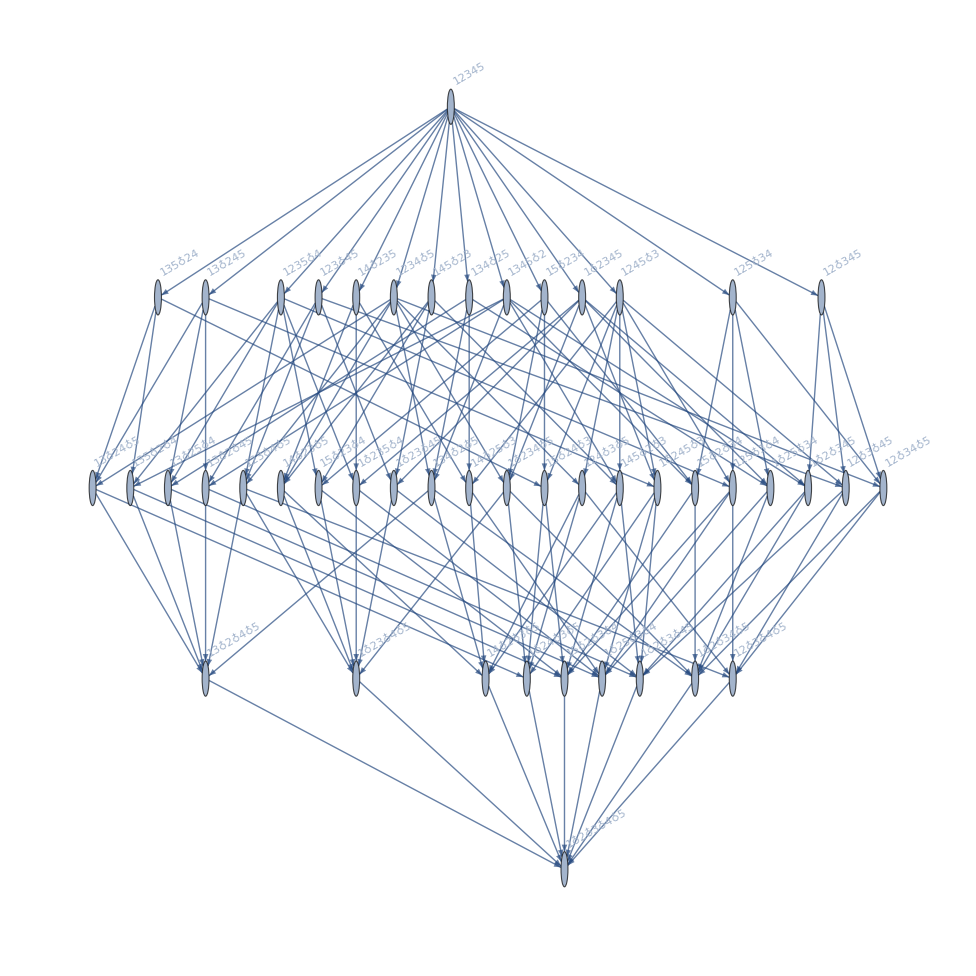

```mathematica
FindEmptyFormula[MinimalGraph[4]]//FormulaGraphReverse
```

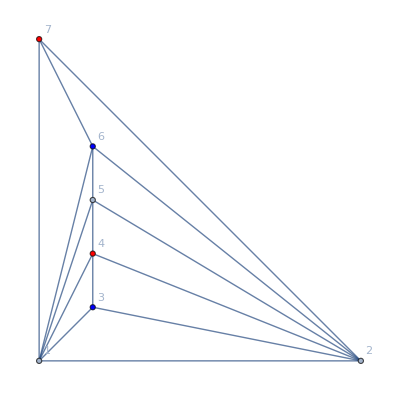

```mathematica
Graph[MinimalGraph[6],VertexStyle->{3 -> Blue, 6 -> Blue,4 -> Red, 7 -> Red}]
```

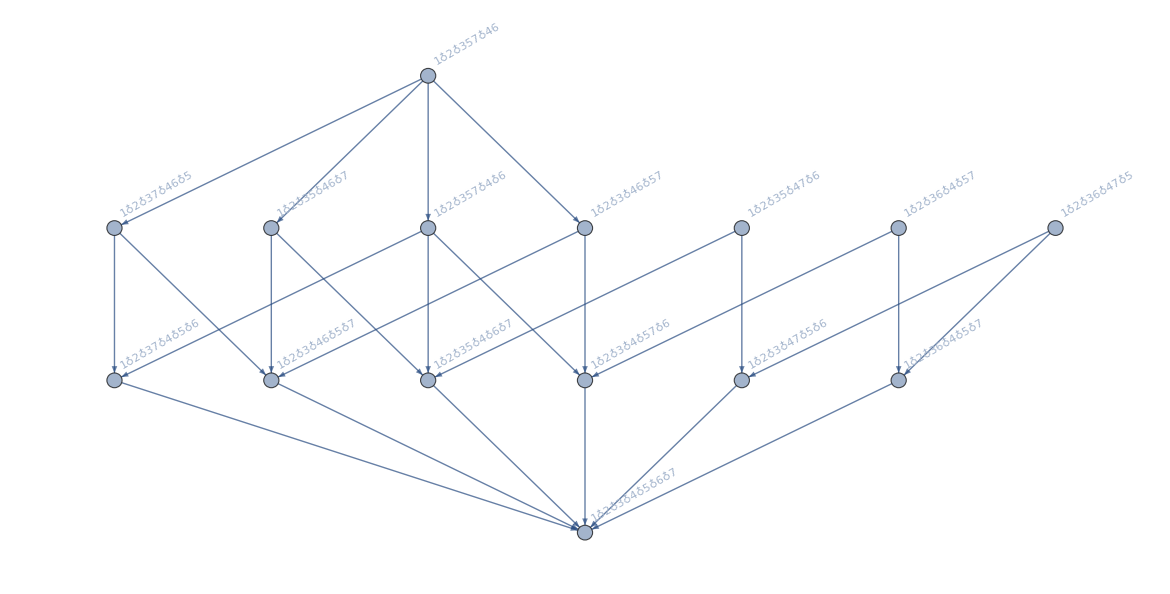

```mathematica
FindFullFormula[MinimalGraph[6]]//FormulaGraphReverse
```

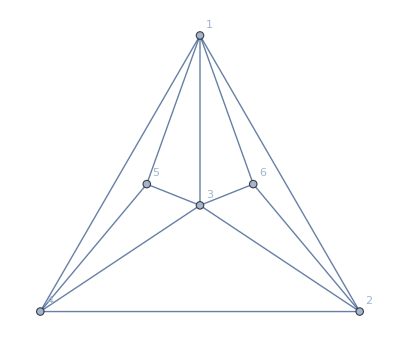

```mathematica
Graph[{1<->2,2<->3,1<->3,1<->4,2<->4,4<->3,1<->5,3<->5,4<->5,1<->6,2<->6,3<->6},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
SetsToColors[sets_]:=Block[{colors={Red,Blue,Green,Yellow,White,Black,Cyan},i,result={}},
For[i=1,i≤Length[sets],i++,
result=Join[result,Table[v->colors[[i]],{v,sets[[i]]}]]
];
result
]
```

```mathematica
SetsToColors[SymbolToSets[v1x2x3x4x5x67]]
```

{1→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],3→RGBColor[0, 1, 0],4→RGBColor[1, 1, 0],5→GrayLevel[0],6→RGBColor[0, 1, 1],7→RGBColor[0, 1, 1]}

```mathematica
SetsToColors[v17x25x3x46]
```

{}

```mathematica
Select[FindFullFormula[Graph[{1<->2,2<->3,1<->3,1<->4,2<->4,4<->3,1<->5,3<->5,4<->5,1<->6,2<->6,3<->6,3<->7,2<->7,4<->7}]],SymbolLevel[#]==5&]
```

{v1x2x3x4x567,v1x2x3x46x57,v1x25x3x4x67,v1x25x3x46x7,v17x2x3x4x56,v17x2x3x46x5,v17x25x3x4x6}

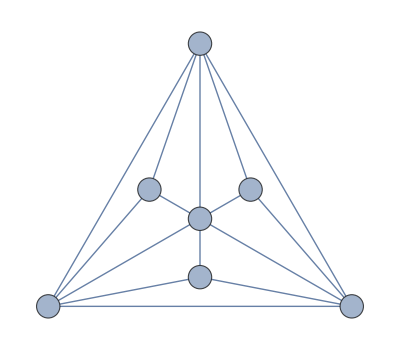
{-Graphics-1♁2♁3♁4♁567,-Graphics-1♁2♁3♁46♁57,-Graphics-1♁25♁3♁4♁67,-Graphics-1♁25♁3♁46♁7,-Graphics-17♁2♁3♁4♁56,-Graphics-17♁2♁3♁46♁5,-Graphics-17♁25♁3♁4♁6,-Graphics-17♁25♁3♁46}

```mathematica
With[
{g=Graph[{1<->2,2<->3,1<->3,1<->4,2<->4,4<->3,1<->5,3<->5,4<->5,1<->6,2<->6,3<->6,3<->7,2<->7,4<->7}]},
Table[Labeled[Graph[g,VertexStyle->SetsToColors[SymbolToSets[s]],GraphLayout->"TutteEmbedding",VertexSize ->Large],SymbolToLabel[s]],
{s,Select[FindFullFormula[g],SymbolLevel[#]<=5&]}]
]
```

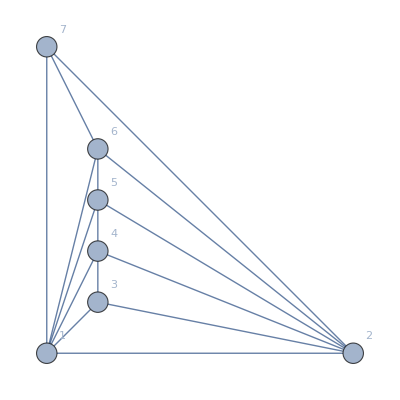
{-Graphics-1♁2♁3♁46♁57,-Graphics-1♁2♁37♁46♁5,-Graphics-1♁2♁36♁4♁57,-Graphics-1♁2♁36♁47♁5,-Graphics-1♁2♁357♁4♁6,-Graphics-1♁2♁35♁47♁6,-Graphics-1♁2♁35♁46♁7,-Graphics-1♁2♁357♁46}

```mathematica
With[
{g=MinimalGraph[6]},
Table[Labeled[Graph[g,VertexStyle->SetsToColors[SymbolToSets[s]],GraphLayout->"PlanarEmbedding",VertexSize ->Large],SymbolToLabel[s]],
{s,Select[FindFullFormula[g],SymbolLevel[#]<=5&]}]
]
```

```mathematica
FindFullFormula[Graph[{1<->2,2<->3,1<->3,1<->4,2<->4,4<->3,1<->5,3<->5,4<->5,1<->6,2<->6,3<->6,3<->7,2<->7,4<->7}]]
```

{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x57x6,v1x2x3x4x56x7,v1x2x3x4x567,v1x2x3x46x5x7,v1x2x3x46x57,v1x25x3x4x6x7,v1x25x3x4x67,v1x25x3x46x7,v17x2x3x4x5x6,v17x2x3x4x56,v17x2x3x46x5,v17x25x3x4x6,v17x25x3x46}

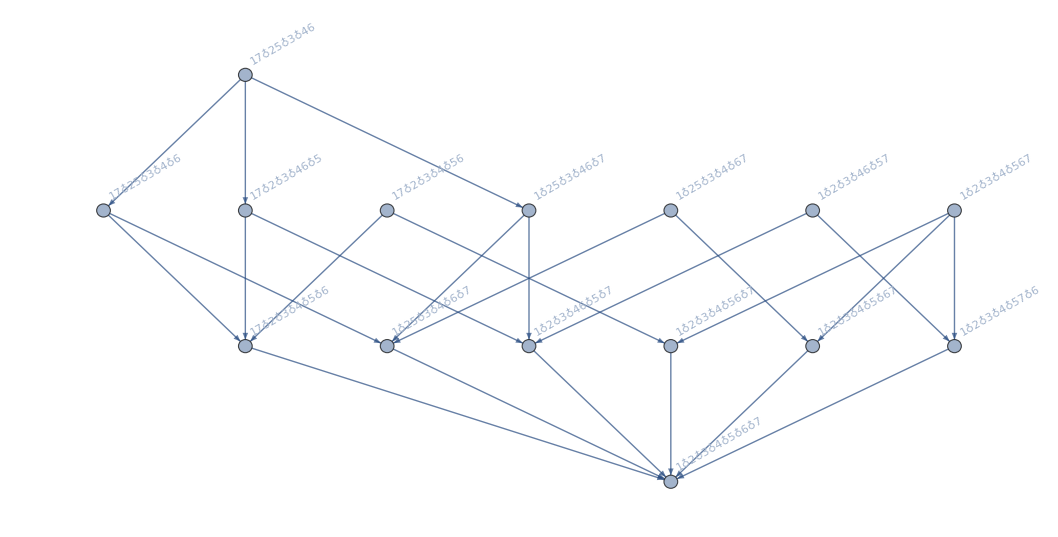

```mathematica
FindFullFormula[Graph[{1<->2,2<->3,1<->3,1<->4,2<->4,4<->3,1<->5,3<->5,4<->5,1<->6,2<->6,3<->6,3<->7,2<->7,4<->7}]]//FormulaGraphReverse
```



```mathematica
Graph[{1<->2,2<->3,1<->3}]
```